21.7021

{7.44382964944677815×10^-9,4.5214643903313283×10^-9,2.73675540935631×10^-9,1.650698268523698×10^-9,9.92144450660758×10^-10,5.9423507263381×10^-10,3.5466510950703×10^-10,2.109386105216×10^-10,1.25017737859×10^-10,7.38355194573×10^-11,4.345467135×10^-11,2.548482564×10^-11,1.48932566×10^-11,8.67213083×10^-12,5.0302014×10^-12,2.9043707×10^-12,1.665571×10^-12,9.42187×10^-13,5.14195×10^-13,2.4952×10^-13}

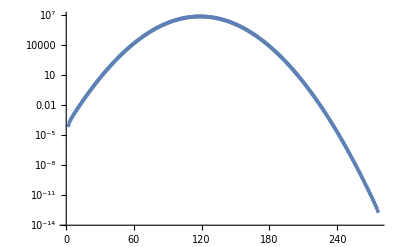

```mathematica
mass=2;
V[r_]=(r-15)^2;
xmin=10;
xmax=20;
nOfPoints=236;
stepSize=(xmax-xmin)/(nOfPoints-1);

(* xmax = 20 *)
extraPoints=0;
energy=0.4998868009845387437379292574102`110;

(* xmax = 20.425531914893618 *)
extraPoints=10;
energy=0.4998868009845387437370223`110;

(* xmax =  20.851063829787236*)
extraPoints=20;
energy=0.49988680098453874373702219283`110;

(* xmax =  21.27659574468085*)
extraPoints=30;
energy=0.4998868009845387437370221928276847`120;

(* xmax = 21.702127659574465 *)
extraPoints=40;
energy=0.49988680098453874373702219282768428907`120;

xmin+(xmax-xmin)/(nOfPoints-1.)(nOfPoints-1+extraPoints)
Q[r_]=2mass*(energy-V[r]);
ψ=Table[0,{nOfPoints+extraPoints}];
ψ[[1]]=0;
ψ[[2]]=10^-4;
Do[ψ[[j+1]]=ψ[[j]](2-stepSize^2*Q[xmin +stepSize(j-1)])-ψ[[j-1]],{j,2,nOfPoints-1+extraPoints}];
(* integral=(Sum[ψ[[j]]^2,{j,2,nOfPoints-1}]+ψ[[nOfPoints]]^2/2)stepSize
ψ=ψ/√integral;*)
 Take[ψ,-20]
ListLogPlot[Abs[ψ]]
```

```mathematica
f=Interpolation[Table[{xmin +stepSize(j-1),ψ[[j]]},{j,1,nOfPoints}],InterpolationOrder->3,Method->"Spline"];
```

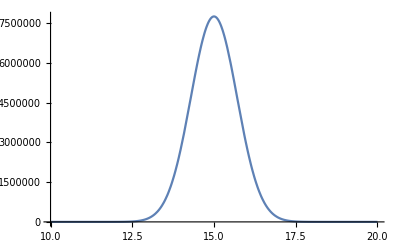

```mathematica
Plot[f[x],{x,10,20},PlotRange->All]
```

```mathematica
data={{0,0.4998868009845387437379292574102`110},{10,0.4998868009845387437370223`110},{20,0.49988680098453874373702219283`110},{30,0.4998868009845387437370221928276847`120},{40,0.49988680098453874373702219282768428907`120}};
```

```mathematica
rule={x_,y_}->{x,y-0.49988680098453874373702219282768428907`120};
data/.rule
```

{{0,9.0706458251571093×10^-22},{10,1.0717231571093×10^-25},{20,2.31571093×10^-30},{30,4.1093×10^-34},{40,0.}}